```mathematica
myModel[populationSize_,mutationRate_,selectionStrength_]:=(
(*Set initial condition*)
frequency1=0.1; (*frequency of the allele to be followed (A)*)
numberOfGenerations=40000;

(*Initialise list in which we will save the frequencies from every pokolenie*)
frequencies=Table[0,{numberOfGenerations}];
For[i=1, i≤ numberOfGenerations, i++,
(*mutation*)
frequency1=mutationRate*(1-frequency1)+(1-mutationRate)*frequency1;
(*selection*)
frequency1=frequency1*(1-selectionStrength)/((1-selectionStrength)*frequency1+(1-frequency1));
(*sampling*)
Na=RandomVariate[BinomialDistribution[populationSize,frequency1]];
frequency1=Na/populationSize;
(*saving values*)
frequencies[[i]]=frequency1;
];
ListPlot[frequencies,PlotRange->Automatic]
)
```

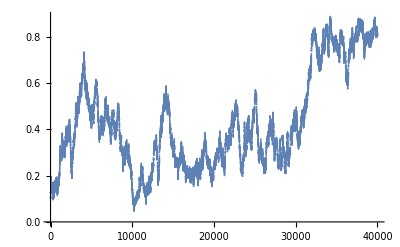

```mathematica
myModel[10000,0.0001,0]
```